```mathematica
Table[
three=Monitor[Table[Chrom3[k],{k,1,max}],{k,N[k/max * 100]}];
Print["Saving D:\\three" <> ToString[max]<> ".m"];
Save["D:\\three" <> ToString[max]<> ".m",{three}]; Print[max];max,
{max,Range[250000,375000,25000]}
]
```

Saving D:\three250000.m

250000

Saving D:\three275000.m

275000

Saving D:\three300000.m

300000

Saving D:\three325000.m

325000

Saving D:\three350000.m

350000

Saving D:\three375000.m

375000

```mathematica
three=Monitor[Table[Chrom3[k],{k,1,398438}],{k,N[k/398438 * 100]}]
```

{0,0,0,6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,398120,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6,0}
 |  |  |  |

```mathematica
Save["D:\\three398438.m",{three}];
```

```mathematica
$HistoryLength=3
```

3

```mathematica
Table[
three=Monitor[Table[Chrom3[k],{k,1,max}],{k,N[k/max * 100]}];
Print["Saving D:\\three" <> ToString[max]<> ".m"];
Save["D:\\three" <> ToString[max]<> ".m",{three}]; Print[max];max,
{max,Range[325000,375000,25000]}
]
```

```mathematica
three=Monitor[Table[Chrom3[k],{k,1,max}],{k,N[k/max * 100]}];
```

```mathematica
Length[three]
```

398438

```mathematica
Clear[Chrom3]
```

```mathematica
Select[
Monitor[
Table[{k,Chrom3[k]},{k,1,Length[three]}],
k],
#[[2]]≠0&
]
```

{{4,6},{21,6},{62,6},{233,6},{305,6},{817,6},{1349,6},{3837,6},{5784,6},{6273,6},{6986,6},{7235,6},{8528,6},{8645,6},{9149,6},{11260,6},{26647,6},{29694,6},{30362,6},{46084,6},{50958,6},{50971,6},{57272,6},{63593,6},{68602,6},{87555,6},{92194,6},{92195,6},{139512,6},{145116,6},{149903,6},{166336,6},{172175,6},{175594,6},{211523,6},{211803,6},{213783,6},{225920,6},{243845,6},{278314,6},{280562,6},{318689,6},{319127,6},{319133,6},{321467,6},{335864,6},{365397,6},{368717,6},{375824,6},{394433,6},{394786,6},{394790,6},{394796,6},{395199,6},{398437,6}}

```mathematica
Table[
VertexCount[ReadGrof[rec[[1]]]],
{rec,{{4,6},{21,6},{62,6},{233,6},{305,6},{817,6},{1349,6},{3837,6},{5784,6},{6273,6},{6986,6},{7235,6},{8528,6},{8645,6},{9149,6},{11260,6},{26647,6},{29694,6},{30362,6},{46084,6},{50958,6},{50971,6},{57272,6},{63593,6},{68602,6},{87555,6},{92194,6},{92195,6},{139512,6},{145116,6},{149903,6},{166336,6},{172175,6},{175594,6},{211523,6},{211803,6},{213783,6},{225920,6},{243845,6},{278314,6},{280562,6},{318689,6},{319127,6},{319133,6},{321467,6},{335864,6},{365397,6},{368717,6},{375824,6},{394433,6},{394786,6},{394790,6},{394796,6},{395199,6},{398437,6}}}
]//Tally
```

```mathematica
Map[{#[[1]],Log[2,#[[2]]]}&,{{6,1},{8,1},{9,1},{10,2},{11,2},{12,8},{13,8},{14,32}}]
```

{{6,0},{8,0},{9,0},{10,1},{11,1},{12,3},{13,3},{14,5}}

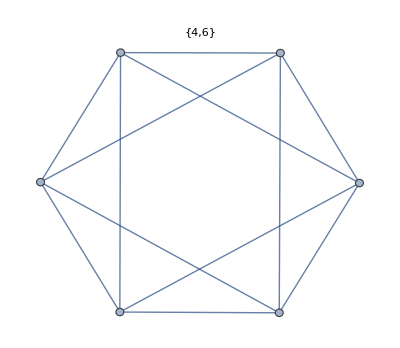
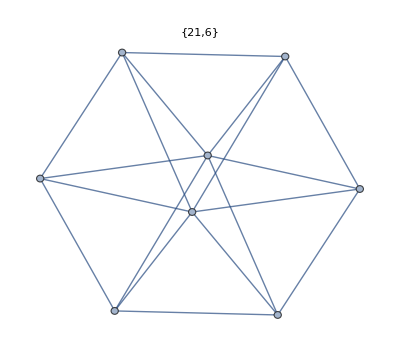
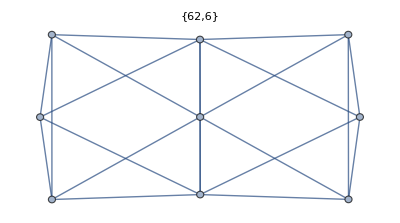
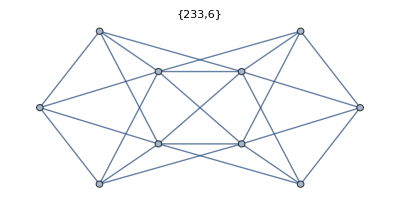
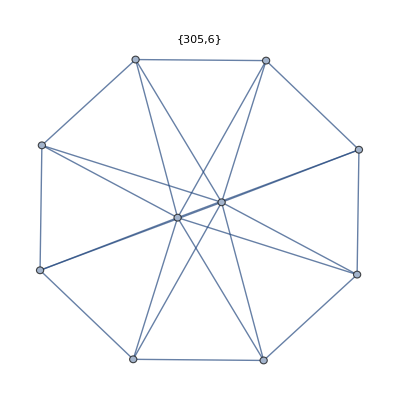
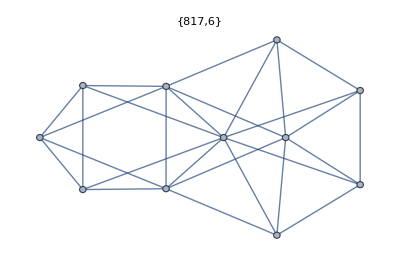
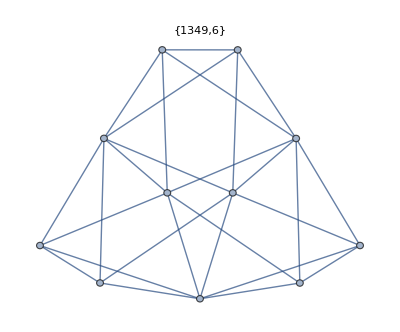
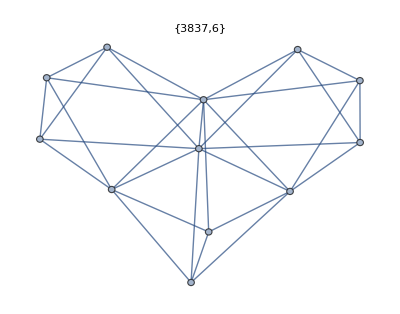

```mathematica
Table[
Graph[ReadGrof[rec[[1]]], PlotLabel->rec],
{rec,{{4,6},{21,6},{62,6},{233,6},{305,6},{817,6},{1349,6},{3837,6},{5784,6},{6273,6},{6986,6},{7235,6},{8528,6},{8645,6},{9149,6},{11260,6},{26647,6},{29694,6},{30362,6},{46084,6},{50958,6},{50971,6},{57272,6},{63593,6},{68602,6},{87555,6},{92194,6},{92195,6},{139512,6},{145116,6},{149903,6},{166336,6},{172175,6},{175594,6}}}
]
```

```mathematica
JacobsThalQ[ReadGrof[9149]]
```

True